# Powerplay

Evolutionary powerplay for Nascence materials

This example contains a search for classifiers

```mathematica
Row[{Style["Jan Koutnik, IDSIA, E-mail:  ",FontFamily->"Roman",FontSize->16],DynamicModule[{r="@"->".",bt,b=Button[bt,b=Hyperlink["mailto:"~~StringReplace[bt,{r,Reverse@r}]]]},bt="hkou.idsia@ch";Dynamic@b]}]
```

Jan Koutnik, IDSIA, E-mail:

## Imports

```mathematica
Import["../libMLP/bp9.m"]
```

```mathematica
Import["../libNES/nes10.m"]
```

```mathematica
Import["../libCoSyNE/libCosyne9.m"]
```

## VM

Vitual material is a simple MLP here :

```mathematica
actF:=2/(1+Exp[-#])-1&
```

```mathematica
actF=Tanh;
```

```mathematica
vm=randomNet[{10,50,20,1}];
```

```mathematica
evalVM[vm_,x_]:=Last@fwdPass[vm,x]
```

```mathematica
res=Sort@Flatten[evalVM[vm,#]&/@RandomReal[{-1,1},{500,10}]];
Min@res
Max@res
```

-0.972087

0.957285

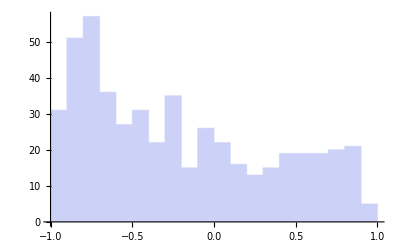

```mathematica
Histogram[res,20]
```

```mathematica
evalVM[vm_,config_,input_]:=evalVM[vm,Join[config,input]]
```

```mathematica
plotBounds[vm_,config_,set_]:=With[{points=(First/@#)&/@SortBy[GatherBy[set,Last],#⟦1,2,1⟧&]},Show[{
ContourPlot[evalVM[vm,config,{x,y}],{x,-1,1},{y,-1,1},Contours->{0},ContourShading->{LightRed,LightGreen},ContourStyle->Directive[Black,Dashed],FrameTicks->False,ImageSize->100],
ListPlot[points,PlotStyle->{Darker@Red,Darker@Green}]
}]]
```

```mathematica
evalVM[vm,config,{1,1}]
```

{-0.601582}

```mathematica
plotBounds[vm,config,trainingSet]
```

-Graphics-

## Powerplay Example - 2-space Classifiers

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/koutnij/Dropbox/math/nascence

In this example a space of classifiers is explored.

```mathematica
maxTasks=1000;
```

```mathematica
SeedRandom[30];
taskSet=RandomReal[{-1,1},{maxTasks,2}];
```

```mathematica
currentTask=1;
```

First point in the task set :

```mathematica
trainingSet={{taskSet⟦1⟧,{1}}}
```

{{{-0.71618,0.607906},{1}}}

```mathematica
trainingSet={{taskSet⟦1⟧,{1}},{taskSet⟦2⟧,{-1}},{taskSet⟦3⟧,{1}},{taskSet⟦4⟧,{-1}},{taskSet⟦5⟧,{1}},{taskSet⟦6⟧,{-1}},{taskSet⟦7⟧,{1}},{taskSet⟦8⟧,{-1}}};
```

XOR :

```mathematica
xorSet=MapThread[Append[{#1},{#2}]&,{Tuples[{-.9,.9},2],{-1,1,1,-1}}]
```

{{{-0.9,-0.9},{-1}},{{-0.9,0.9},{1}},{{0.9,-0.9},{1}},{{0.9,0.9},{-1}}}

```mathematica
trainingSet=xorSet;
```

```mathematica
fitFn[g_,set_]:=With[{diff=Flatten[(evalVM[vm,g,#]&/@set⟦All,1⟧)-set⟦All,2⟧]},Total[diff^2]]
```

```mathematica
fitFn[g_]:=fitFn[g,trainingSet]
```

```mathematica
solvesAllTasksQ[g_,set_]:=Equal[Sign@Flatten[(evalVM[vm,g,#]&/@set⟦All,1⟧)],Flatten@set⟦All,2⟧]
```

```mathematica
solvesAllTasksQ[g_]:=solvesAllTasksQ[g,trainingSet]
```

```mathematica
optimize[pop_,fitFn_,trainingSet_,nGen_]:=Module[{popTmp},NestWhile[(popTmp=coSyNEstep[#,fitFn[#,trainingSet]&,minimize->True,mutate->0.8,permuteAll->True,verbose->False,elite->1];Print[{popTmp⟦1,1⟧,solvesAllTasksQ[popTmp⟦1,2⟧,trainingSet]}];Print@plotBounds[vm,popTmp⟦1,2⟧,trainingSet];popTmp)&,pop,Not[solvesAllTasksQ[#⟦1,2⟧,trainingSet]]&,1,
nGen]]
```

```mathematica
reevaluate[pop_,fitFn_]:=SortBy[{fitFn[#],#}&/@pop⟦All,2⟧,First]
```

```mathematica
appendTask[set_,config_]:=With[{point=taskSet⟦Length[set]+1⟧},Append[set,{point,-Sign[evalVM[vm,config,point]]}]]
```

```mathematica
powerplay[fitFn_,popSize_,nGen_,nTasks_]:=Module[{pop,set},
set={{taskSet⟦1⟧,{1}}};(*first task*)
pop=SortBy[newRandomPop[popSize,dim,NormalDistribution[0,1],fitFn[#,set]&],First];
Print["Generated population"];
Nest[
(Print["# of tasks : "<>ToString@Length[set]];
pop=optimize[pop,fitFn,set,nGen];(*optimize*)
set=appendTask[set,pop⟦1,2⟧];(*add next task*)
pop=reevaluate[pop,fitFn[#,set]&];
pop)&
,pop,nTasks]
]
```

## Example Experiment

Powerplay with population size of 8, 30 generations of CoSyNE and 10 consecutive classification tasks to solve :

```mathematica
powerplay[fitFn,8,30,10]
```

Generated population

# of tasks : 1

# of tasks : 2

{2.34823,False}

-Graphics-

{2.09571,False}

-Graphics-

{2.00215,False}

-Graphics-

{1.91676,False}

-Graphics-

{1.91676,False}

-Graphics-

{1.69548,False}

-Graphics-

{1.69548,False}

-Graphics-

{1.69548,False}

-Graphics-

{1.5368,True}

-Graphics-

# of tasks : 3

{2.30423,False}

-Graphics-

{2.30423,False}

-Graphics-

{2.30423,False}

-Graphics-

{2.28959,False}

-Graphics-

{2.28359,False}

-Graphics-

{2.23056,False}

-Graphics-